```mathematica
m={{0, Cos[k1],Cos[k2]},{Cos[k1],0,Cos[k1-k2]},{Cos[k2],Cos[k1-k2],0}}
```

{{0,Cos[k1],Cos[k2]},{Cos[k1],0,Cos[k1-k2]},{Cos[k2],Cos[k1-k2],0}}

```mathematica
MatrixForm[m]
```

(0 | Cos[k1] | Cos[k2]
Cos[k1] | 0 | Cos[k1-k2]
Cos[k2] | Cos[k1-k2] | 0)

```mathematica
Eigenvalues[m]
```

{-1,1/2 (1-√(3+2 Cos[2 k1]+2 Cos[2 k1-2 k2]+2 Cos[2 k2])),1/2 (1+√(3+2 Cos[2 k1]+2 Cos[2 k1-2 k2]+2 Cos[2 k2]))}

```mathematica
e[k1_,k2_,z_]:=1/2+z/2Sqrt[3+2Cos[k1]+2Cos[k1/2+Sqrt[3]/2 k2] +2Cos[k1/2+Sqrt[3]k2]]
```

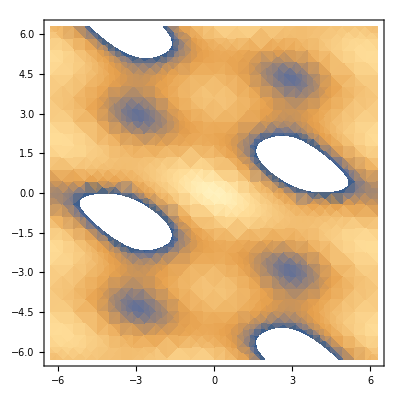

```mathematica
DensityPlot[e[k1,k2,1],{k1,-2Pi,2Pi},{k2,-2Pi,2Pi}]
```

```mathematica
Plot3D[{e[k1,k2,1],e[k1,k2,-1]},{k1,-2Pi,2Pi},{k2,-2Pi,2Pi},AxesLabel->{"k_1","k_2","E"}]
```

-Graphics3D-

```mathematica
c1[t_]:=Pi{1/3,1/Sqrt[3]}t
```

```mathematica
c2[t_]:=Pi{1/3,1/Sqrt[3]}(2-t)+Pi{2/3,0}(t-1)
```

```mathematica
c3[t_]:=Pi{2/3,0}(3-t)+{0,0}(t-2)
```

```mathematica
c[t_]:=Piecewise[{{c1[t],t<1},{c2[t],t<2},{c3[t],t≤3}}]
```

```mathematica
c[t]
```

Piecewise[{{{(π t)/3,(π t)/(√3)}, t<1}, {{1/3 π (2-t)+2/3 π (-1+t),(π (2-t))/(√3)}, t<2}, {{2/3 π (3-t),0}, t≤3}, {0, True}}]

```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

```mathematica
c1[t][[1]]
```

(π t)/3

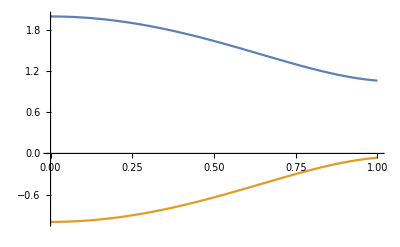

```mathematica
Plot[{e[c1[t][[1]],c1[t][[2]],1],e[c1[t][[1]],c1[t][[2]],-1]},{t,0,1}]
```

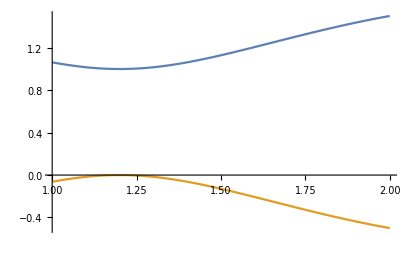

```mathematica
Plot[{e[c2[t][[1]],c2[t][[2]],1],e[c2[t][[1]],c2[t][[2]],-1]},{t,1,2}]
```

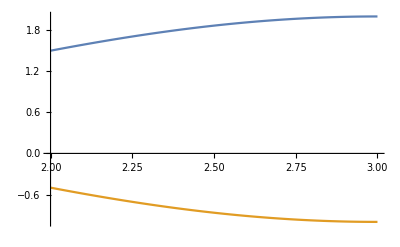

```mathematica
Plot[{e[c3[t][[1]],c3[t][[2]],1],e[c3[t][[1]],c3[t][[2]],-1]},{t,2,3}]
```

Plot::exclul: {Im[4 Cos[(π t)/6]+2 Cos[(π t)/3]]-0,Im[4 Cos[1/2 Power[«2»] π t]+2 Cos[Power[«2»] π t]]-0,Im[4 Cos[1/2 Less[«2»]]+2 Cos[t<1]]-0,Im[4 Cos[1/2 Plus[«2»]]+2 Cos[Times[«3»]+Times[«3»]]]-0,Im[4 Cos[1/2 «2» Plus[«2»]]+«1»]-0,Im[4 Cos[1/2 Less[«2»]]+2 Cos[t<2]]-0,Im[4 Cos[1/3 π Plus[«2»]]+2 Cos[2/3 π Plus[«2»]]]-0,Im[4 Cos[1/2 LessEqual[«2»]]+2 Cos[t≤3]]-0} must be a list of equalities or real-valued functions.

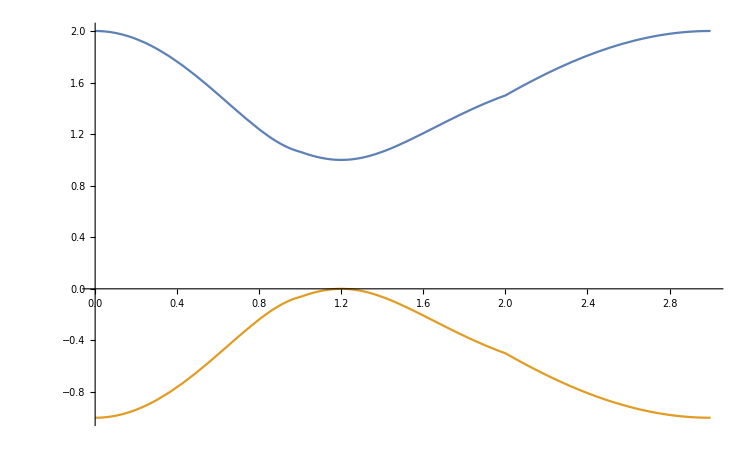

```mathematica
Plot[{e[c[t][[1]],c[t][[2]],1],e[c[t][[1]],c[t][[2]],-1]},{t,0,3}]
```

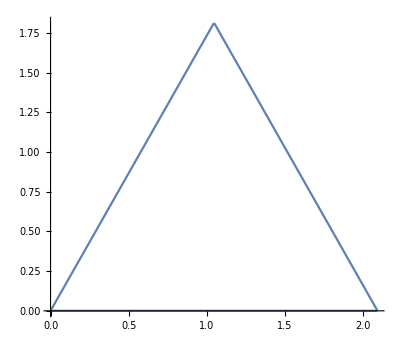

```mathematica
ParametricPlot[c[t],{t,0,3}]
```

```mathematica
ee[t_]:=e[c[t][[1]],c[t][[2]],1]
```

```mathematica
e[c1[x][[1]],c1[x][[2]],1]//CForm
```

0.5 + Sqrt(3 + 2*Cos((Pi*x)/3.) + 2*Cos((2*Pi*x)/3.) + 2*Cos((7*Pi*x)/6.))/2.

```mathematica
e[c2[x][[1]],c2[x][[2]],1]//CForm
```

0.5 + Sqrt(3 + 2*Cos(((Pi*(2 - x))/3. + (2*Pi*(-1 + x))/3.)/2. + (Pi*(2 - x))/2.) + 
      2*Cos(((Pi*(2 - x))/3. + (2*Pi*(-1 + x))/3.)/2. + Pi*(2 - x)) + 
      2*Cos((Pi*(2 - x))/3. + (2*Pi*(-1 + x))/3.))/2.

```mathematica
e[c3[x][[1]],c3[x][[2]],1]//CForm
```

0.5 + Sqrt(3 + 4*Cos((Pi*(3 - x))/3.) + 2*Cos((2*Pi*(3 - x))/3.))/2.